THE FOLLOWING ASSUMES THAT IMPORTED DATA IS IN A TSV FORMAT OF THE FOLLOWING STYLE: X VX Y VY WITH INTEGER FREQUENCIES SERVING AS THE SEPARATION BETWEEN DIFFERENT SIMULATIONS.  CHANGES TO THIS CODE MUST TAKE THIS INTO CONSIDERATION

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*200 volt data*)
lowFieldMPI=Import["low-field-200-V-MPI.tsv"];
moreData=Import["low-field-200-V-MPI-more.tsv"];
lowFieldMPI=Join[lowFieldMPI,moreData];
lowFieldAlt=Import["low-field-200-V-Alt.tsv"];
highFieldMPI=Import["High-field-MPI.tsv"];
highFieldAlt=Import["high-field-Alt.tsv"];
```

--This first function(getIndices) finds how many frequencies were tested in the data set.

--This function(plotVData) makes plots of Vy v. Vx for each frequency and places them in a list. Converts to m/s
 
--The count function counts how many particles survived for each frequency (Here the frequency is in kHz and as an optional argument one can provide the number of particles simulated to compute the success rate instead of particle count.
         
--The plotPhaseSpaceXData makes phase space plots of Vx v x.

--The findPeakFreq function sorts through the data to find the frequency at which maximum trapping occurs. It also returns the position of the data point in the count list.
The format being {index, {frequency,count}}

--The maxBoltz function is also here to plot theoretical Maxwellian distributions on histograms. MAKE SURE THAT IF YOU ARE USING A DIFFERENT MASS THAT YOU ALTER THE MATH PARAMETER IN THE FUNCTION!!!

--The speedToTemp function takes the average speed of the molecules and calculates the temperature.

```mathematica
getIndices[data_]:=Module[{i=1,indices={}},
While[i≤Length[data],
If[Mod[data⟦i,1⟧,1]==0,
AppendTo[indices,i];
];
i++;
];
Return[indices];
]
```

```mathematica
plotVData[data_]:=Module[{vList={},vPlots={},i,indexList,k=0,freq},
indexList=getIndices[data];
freq=data⟦1,1⟧;

For[i=1,i≤ Length[data],i++,
If[MemberQ[indexList,i]==False,
AppendTo[vList,{data⟦i,2⟧,data⟦i,4⟧}*1000];
];
If[MemberQ[indexList,i],
AppendTo[vPlots,ListPlot[vList,PlotLabel->ToString[k]<>", "<>ToString[freq]]];
k++;
freq=data⟦i,1⟧;
vList={};
];
If[i==Length[data],
AppendTo[vPlots,ListPlot[vList,PlotLabel->ToString[k]<>", "<>ToString[freq]]];
]
];

Return[Drop[vPlots,1]]
]
```

```mathematica
count[data_,initNumber_:1]:=Module[{counts=0,countList={},i,indexList,freq},
indexList=getIndices[data];
freq=data⟦1,1⟧;

For[i=1,i≤ Length[data],i++,

If[MemberQ[indexList,i] && i≠1,
AppendTo[countList,{freq/1000,counts/initNumber}];
freq=data⟦i,1⟧;
counts=0;
];

If[MemberQ[indexList,i]==False,
counts++;
];

If[i==Length[data],
AppendTo[countList,{data⟦Last[indexList],1⟧/1000,counts/initNumber}];
];

];

Return[countList]
]
```

```mathematica
plotPhaseSpaceYData[data_]:=Module[{psList={},psPlots={},i,indexList},
indexList=getIndices[data];

For[i=1,i≤ Length[data],i++,
If[MemberQ[indexList,i]==False,
AppendTo[psList,{data⟦i,3⟧,1000*data⟦i,4⟧}];
];
If[MemberQ[indexList,i],
AppendTo[psPlots,ListPlot[psList,Frame->True,FrameLabel->{"y(mm)","Vy(m/s)"},ImageSize->Medium,PlotRange->{{0,.05},{-20,20}},AspectRatio->1,LabelStyle->{Black,12},PlotStyle->PointSize[.012]]];
psList={};
];
];

Return[Drop[psPlots,1]]
]
```

```mathematica
plotPhaseSpaceXData[data_]:=Module[{psList={},psPlots={},i,indexList},
indexList=getIndices[data];

For[i=1,i≤ Length[data],i++,
If[MemberQ[indexList,i]==False,
AppendTo[psList,{data⟦i,1⟧,1000*data⟦i,2⟧}];
];
If[MemberQ[indexList,i],
AppendTo[psPlots,ListPlot[psList,Frame->True,FrameLabel->{"x(mm)","Vx(m/s)"},ImageSize->Medium,PlotRange->{{0,.05},{-20,20}},AspectRatio->1,LabelStyle->{Black,12},PlotStyle->PointSize[.012]]];
psList={};
];
];

Return[Drop[psPlots,1]]
]
```

```mathematica
findPeakFreq[data_]:=Module[{i=1,maxTrapped,peakData={},countList},
countList=count[data];
maxTrapped=Max[Transpose[countList]⟦2⟧];
While[True,
If[countList⟦i,2⟧==maxTrapped,
peakData={i,countList⟦i⟧};
Break[];
];
i++;
];
Return[peakData]
]
```

```mathematica
maxboltz1D[v_,T_]:=Module[{m=3.321*10^-26,k=1.38*10^-23,prob},
prob=√(m/(2 π k T)) ⅇ^((-m v^2)/(2 k T));
Return[prob];
]
```

```mathematica
maxboltz[v_,T_]:=Module[{m=3.321*10^-26,k=1.38*10^-23,prob},(*Scaling factor really doesn't matter since I scale the distribution anyways to match the data*)
prob=(m/(2 π k T)) π v^2 ⅇ^((-m v^2)/(2 k T));
Return[prob];
]
```

```mathematica
speedToTemp[v_]:=Module[{k=1.38*10^-23,m=3.321*10^-26,E,T},

T=(.5 m v^2)/k;
Return[T];
]
```

--The getVelocities function grabs all of the velocity data and places it into a list.

--The getPositions function does the same thing but for the positions.

--The getPlotArea function uses a crude method of area approximation to find how much of a space is covered by the data. I would NOT recommend using it.

--The graphPlotAreas function takes the plot areas of the velocity graphs for each frequency measured and graphs the result.

```mathematica
getVelocities[data_]:=Module[{vList={},finalList={},i,indexList},
indexList=getIndices[data];

For[i=1,i≤ Length[data],i++,
If[MemberQ[indexList,i]==False,
AppendTo[vList,{data⟦i,2⟧,data⟦i,4⟧}*1000];
];
If[MemberQ[indexList,i],
AppendTo[finalList,vList];
vList={};
];
If[i==Length[data],AppendTo[finalList,vList];];
];

Return[Drop[finalList,1]]
]
```

```mathematica
getPositions[data_]:=Module[{pList={},finalList={},i,indexList},
indexList=getIndices[data];

For[i=1,i≤ Length[data],i++,
If[MemberQ[indexList,i]==False,
AppendTo[pList,{data⟦i,1⟧,data⟦i,3⟧}];
];
If[MemberQ[indexList,i],
AppendTo[finalList,pList];
pList={};
];
If[i==Length[data],AppendTo[finalList,pList];];
];

Return[Drop[finalList,1]]
]
```

```mathematica
getPlotArea[Data_]:=Module[{x1,x2,y,area=0,i,sortedData},
sortedData=Sort[Data];
For[i=1,i<Length[Data],i++,
x1=sortedData⟦i,1⟧;
x2=sortedData⟦i+1,1⟧;
y=sortedData⟦i,2⟧;
area=area+Abs[y(x2-x1)];
];
Return[area]
]
```

```mathematica
graphPlotAreas[data_]:=Module[{areaList={},i,velocities={},frequencyList},
frequencyList=Transpose[data⟦getIndices[data]⟧]⟦1⟧/1000;
velocities=getVelocities[data];
For[i=1,i≤Length[velocities],i++,
AppendTo[areaList,{frequencyList⟦i⟧,getPlotArea[velocities⟦i⟧]}];
];
Return[ListPlot[areaList,Frame->True,FrameLabel->{"Frequency (kHz)","velocity space area (m^2/s^2)"},PlotLabel->"Velocity Space area v Frequency",ImageSize->Large,Joined->True]]
]
```

The findMaxwellianFit function fits a Maxwellian velocity distribution to a histogram of the velocity data. This gives the approximate temperature T of the successfully trapped molecules in that particular direction. Due to the nature of the HistogramList function I had to drop the first element from histX in order to transpose it with histCount.α simply scales the distribution function up.

```mathematica
findMaxwellianFit[vData_,binWidth_]:=Module[{histDataForVelocities,bestFitForVelocities,bestFitPlot,histX,histCount},{histX,histCount}=HistogramList[Norm/@vData,{0,Max[Norm/@vData],binWidth}];histDataForVelocities=Transpose[{Drop[histX,1],histCount}];bestFitForVelocities=NonlinearModelFit[histDataForVelocities,{α maxboltz[v,T],0<T<0.3},{α,T},v];bestFitPlot=Plot[bestFitForVelocities["BestFit"],{v,0,Max[Norm/@vData]},PlotRange->All];Return[{bestFitForVelocities["BestFitParameters"],Show[{bestFitPlot,ListPlot[histDataForVelocities]}]}]]
```

Here I analyze data for the chip at 200 volts.

```mathematica
lowMPIPlot=ListPlot[count[lowFieldMPI,20000],Joined->True,Frame->True,FrameLabel->{"Frequency (kHz)","Success Rate"},ImageSize->Large,PlotLabel->"Low field in MPI Config"];
lowAltPlot=ListPlot[count[lowFieldAlt,20000],Joined->True,Frame->True,FrameLabel->{"Frequency (kHz)","Success Rate"},ImageSize->Large,PlotLabel->"Low field in Alt Config"];
highMPIPlot=ListPlot[count[highFieldMPI,20000],Joined->True,Frame->True,FrameLabel->{"Frequency (kHz)","Success Rate"},ImageSize->Large,PlotStyle->Red,PlotLabel->"High field in MPI Config"];
highAltPlot=ListPlot[count[highFieldAlt,20000],Joined->True,Frame->True,FrameLabel->{"Frequency (kHz)","Success Rate"},ImageSize->Large,PlotStyle->Red,PlotLabel->"High field in Alt Config"];
```

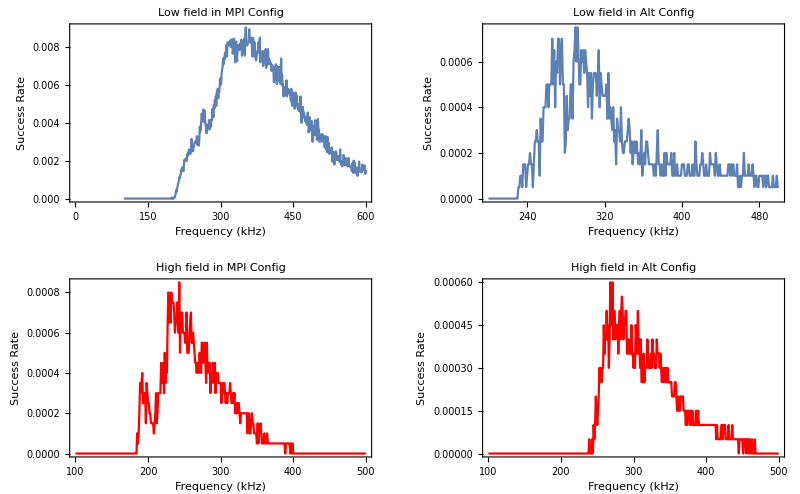

```mathematica
GraphicsGrid[{{lowMPIPlot,lowAltPlot},{highMPIPlot,highAltPlot}},ImageSize->Full]
```

BELOW IS AN ANALYSIS OF THE DATA FOR THE MICROCHIP AT AN OPERATING VOLTAGE OF 650 VOLTS

First, an examination of the successfully trapped molecules. IE. lasting longer than 200 μs.

```mathematica
a=ListPlot[count[lowFieldMPIData,20000],ImageSize->Medium,Frame->True,FrameLabel->{"Frequency (kHz)","Success Rate"},PlotLabel->"Low Field in MPI Config",LabelStyle->{12,Black},Joined->True,PlotRange->All];
```

```mathematica
b=ListPlot[count[highFieldMPIData,20000],ImageSize->Medium,Frame->True,FrameLabel->{"Frequency (kHz)","Success Rate"},Joined->True,PlotStyle->RGBColor[1,0,0],LabelStyle->{12,Black},PlotRange->All,PlotLabel->"High Field in MPI Config"];
```

```mathematica
c=ListPlot[count[lowFieldAltData,20000],LabelStyle->{12,Black},ImageSize->Medium,Frame->True,FrameLabel->{"Frequency (kHz)","Success Rate"},Joined->True,PlotRange->All,PlotLabel->"Low Field in Alt Config"];
```

```mathematica
d=ListPlot[count[highFieldAltData,20000],LabelStyle->{12,Black},ImageSize->Medium,Frame->True,FrameLabel->{"Frequency (kHz)","Success Rate"},Joined->True,PlotRange->All,PlotLabel->"High Field in Alt Config",PlotStyle->RGBColor[1,0,0]];
```

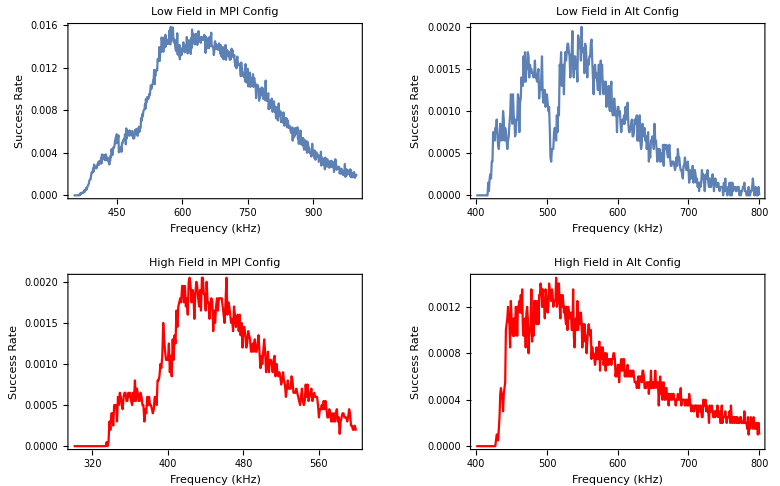

```mathematica
GraphicsGrid[{{a,c},{b,d}},Frame->True]
```

EVERYTHING BELOW THIS POINT IS AN ANALYSIS OF THE TRAPPED MOLECULES IN THE LOW FIELD SEEKING STATE IN THE MPI CONFIGURATION AT 650 VOLTS

These graphs compare the initial velocity sample with the trapped molecule velocities for the low field state using the MPI configuration at 573 kHz

```mathematica
peakVelData=getVelocities[lowFieldMPI]⟦226⟧;
```

```mathematica
peakVx=Histogram[Catenate[ConstantArray[Transpose[peakVelData]⟦1⟧,27]],{-40,40,2},PlotRange->All,PlotLabel->"Final vX * 27",ChartStyle->RGBColor[1,0,0],ImageSize->Large];
```

```mathematica
peakvY=Histogram[Catenate[ConstantArray[Transpose[peakVelData]⟦2⟧,35]],{-40,40,2},PlotRange->{{-40,40},{0,1500}},PlotLabel->"Final vY * 35",ChartStyle->RGBColor[1,0,0],ImageSize->Large];
```

```mathematica
initVx=Histogram[Transpose[initialVelocities]⟦1⟧*1000,{-40,40,2},PlotLabel->"Initial vX v. Final (Red) vX*27",ImageSize->Large];
```

```mathematica
initVy=Histogram[Transpose[initialVelocities]⟦2⟧*1000,{-40,40,2},PlotLabel->"Initial vY v. Final (Red) vY*35",ImageSize->Large];
```

```mathematica
distributionAt300mK=Plot[maxboltz1D[v,.3]*(1550/FindMaximum[maxboltz1D[x,.3],x]⟦1⟧),{v,-40,40}];
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
distributionAtXT=Plot[maxboltz1D[v,.0517]*(1550/FindMaximum[maxboltz1D[x,.0517],x]⟦1⟧),{v,-40,40}];
distributionAtYT=Plot[maxboltz1D[v,.0928]*(1550/FindMaximum[maxboltz1D[x,.0928],x]⟦1⟧),{v,-40,40}];
xComparisonGraphic=Show[{initVx,peakVx,distributionAt300mK,distributionAtXT}];
yComparisonGraphic=Show[{initVy,peakvY,distributionAt300mK,distributionAtYT}];
GraphicsRow[{xComparisonGraphic,yComparisonGraphic}]
```

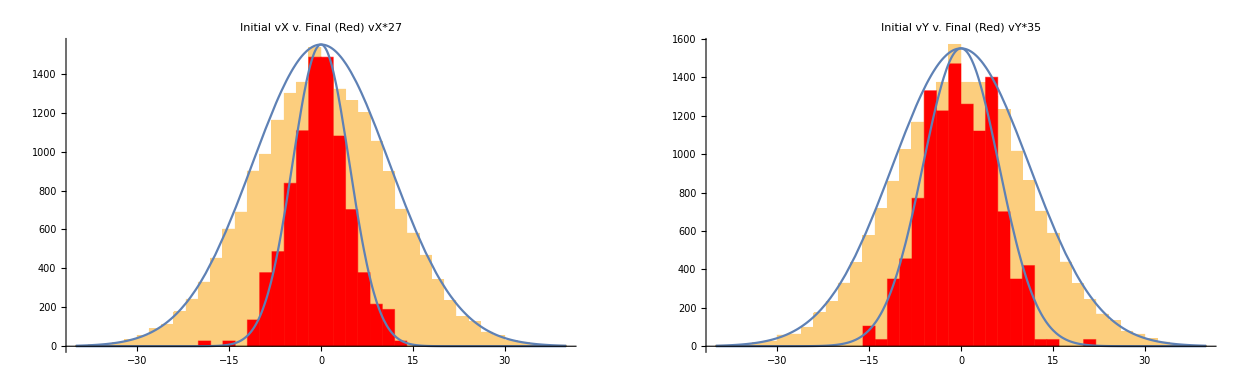

```mathematica
(*I don't like this graph. It's sort of artificial.*)
```

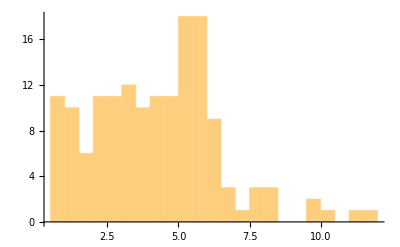

```mathematica
Histogram[Norm/@peakVelData,20]
```

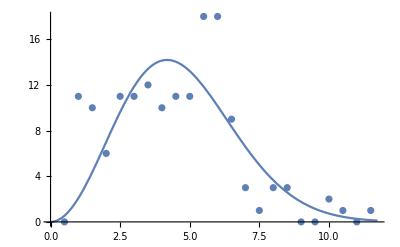
{{α→38.5706,T→0.0210773},-Graphics-}

```mathematica
vfit=findMaxwellianFit[peakVelData,.5]
```

Some position and phase space analysis

```mathematica
peakPosData=getPositions[lowFieldMPIData]⟦226⟧;
```

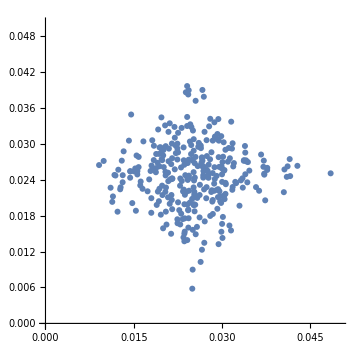

```mathematica
(*initial position plot*)ListPlot[peakPosData,ImageSize->Medium,PlotRange->{{0,.05},{0,.05}},PlotStyle->PointSize[.012],AspectRatio->1]
```

findPeakXpos -- a quick function I wrote to find the particle which has the largest x position. I made this to analyze the anomaly on the position graph

```mathematica
findPeakXpos[posdata_]:=Module[{i=1,maxTrapped,peakData={},countList},
maxTrapped=Max[Transpose[posdata]⟦1⟧];
While[True,
If[posdata⟦i,1⟧==maxTrapped,
peakData={i,posdata⟦i⟧};
Break[];
];
i++;
];
Return[peakData]
]
```

```mathematica
peakXPhaseSpaceData=plotPhaseSpaceXData[lowFieldMPIData];
```

```mathematica
peakYPhaseSpaceData=plotPhaseSpaceYData[lowFieldMPIData];
```

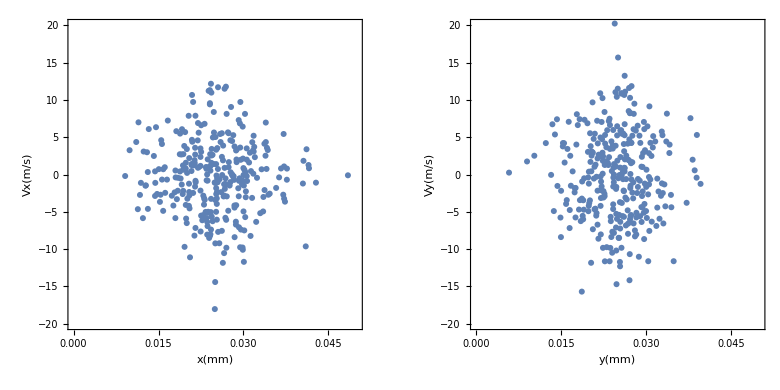

```mathematica
(*phase space graphs*)GraphicsRow[{peakXPhaseSpaceData⟦226⟧,peakYPhaseSpaceData⟦226⟧}]
```

This part compares the trapped particles initial speed to their final speed. We see that they have actually cooled while being in the trap. This was data taken from a test with a voltage of 650 volts.

```mathematica
initialData=Import["old/initParamData.tsv"];
finalData=Import["old/finalParamData.tsv"];
```

```mathematica
initV=getVelocities[initialData]⟦1⟧;
finalV=getVelocities[finalData]⟦1⟧;
```

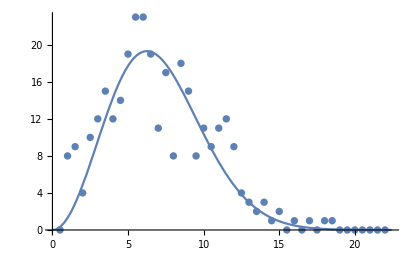
{{α→145.334,T→0.0469596},-Graphics-}

```mathematica
findMaxwellianFit[initV,.5]
```

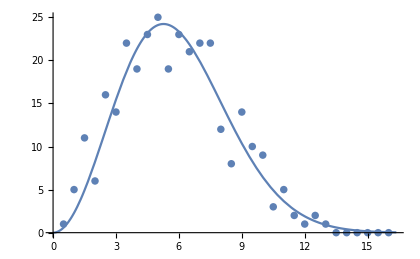
{{α→153.611,T→0.0333682},-Graphics-}

```mathematica
findMaxwellianFit[finalV,.5]
```